```mathematica
img=-Graphics-
```

```mathematica
data=Round[ImageData[img],1]
```

{{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},565,{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},404,{1}}
 |  |  |  |



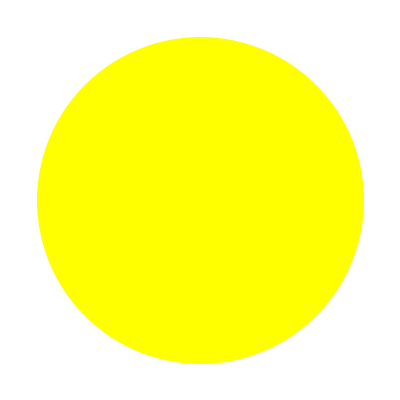
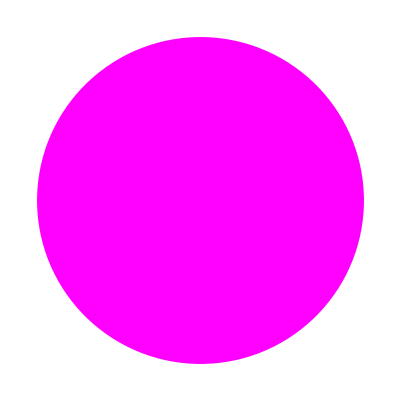
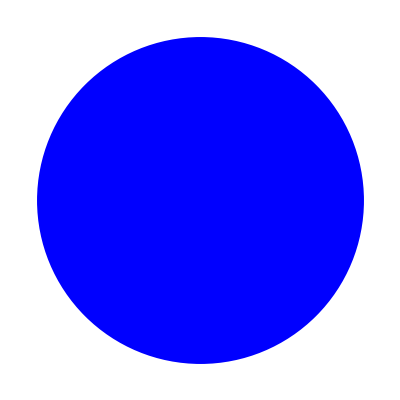
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
col=DeleteDuplicates[Flatten[Round[ImageData[img],1],1]];
Graphics[{RGBColor[#],Disk[]},ImageSize->Tiny]&/@col
```

```mathematica
binImage=Image@Replace[data,{col[[4]]->1,_:>0},{2}]
```

-Graphics-

```mathematica
curve=ImageApply[{0,0,0}&,binImage,Masking->ColorNegate[Binarize[GaussianFilter[binImage,5]]]]
```

-Graphics-

```mathematica
curvLoc=(Reverse/@Position[ImageData[curve,DataReversed->True],{1.,1.,1.}]);
```

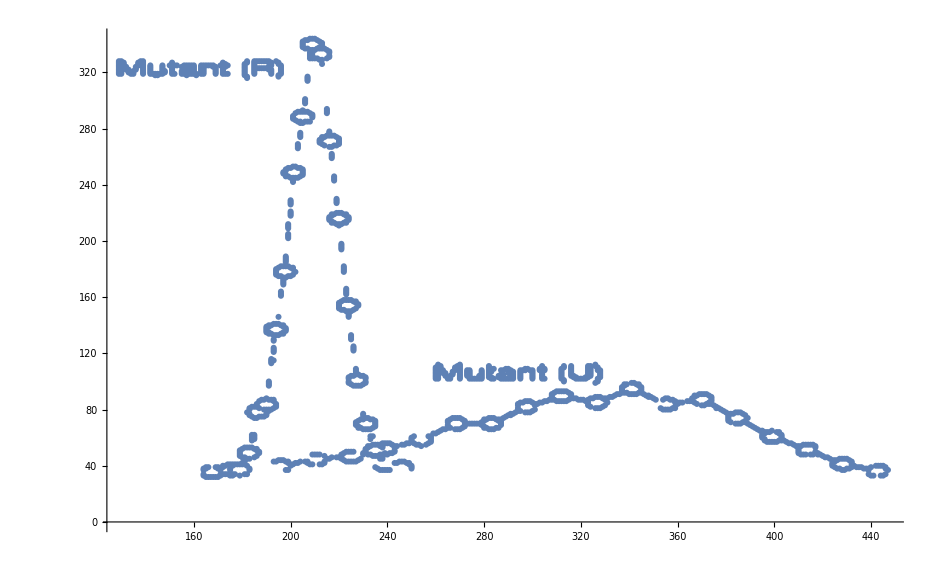

```mathematica
ListPlot[curvLoc,PlotRange->All]
```

```mathematica
forward={{178.89941174504057,37.09855622467808},{182.24349565820032,49.59725999722832},{185.72190260720248,78.29068390872612},{190.10139325498076,84.40099277164154},{193.73651041246572,137.21206109861856},{197.53673296817362,178.884519227},{201.34674991191173,249.3363551358653},{204.47815568498768,289.1329964763761},{208.58060507134098,341.34491577542144},{212.0464192357329,333.43715982871083},{216.31257482201914,271.8562688101932},{219.94489358292407,216.3730463797402},{223.39111897125565,154.2587357625154},{227.32286616622594,100.55526403106626},{231.09230635955328,70.16298717961024},{234.68404837004744,51.06353187993045},{238.16245531904963,40.549351258968386},{245.98257456199934,37.55360611930979}};
```

```mathematica
backward={{195.0685471845695,39.33335681831363},{210.63322896280766,44.20491874584286},{224.84628519288162,46.839152024766236},{239.28741074422976,52.72193594036588},{254.16088856719557,59.02184892604453},{268.3697472023995,70.2084921690734},{283.12429317071314,70.5244990403454},{297.8648471561266,82.00439665991468},{312.0093426699894,89.7705815282954},{326.8226549664841,85.24283507671015},{340.9993320410174,95.46628937610194},{355.2109890728014,83.38218661866057},{369.9697326359851,87.04786632541584},{384.1967808489594,73.63653470863204},{398.721858297709,60.665084656658905},{412.9153257517226,52.37559240945177},{428.4464267710002,41.28248720031934},{442.57413190538256,36.73451630897273}};
```

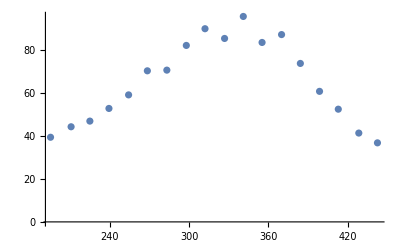

```mathematica
ListPlot@backward
```

```mathematica
MinimalBy[backward,Last]
MinimalBy[forward,Last]
```

{{442.574,36.7345}}

{{178.899,37.0986}}

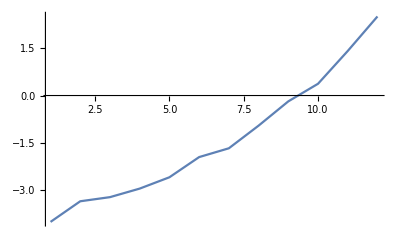

```mathematica
ListLinePlot[Table[-Log[(forward[[i+5,2]]-MinimalBy[backward,Last][[1,2]])/(backward[[i,2]]-MinimalBy[backward,Last][[1,2]])],{i,1,12}],PlotRange->Full]
```

InterpolatingFunction[{{178.899, 245.983}}, <>]

InterpolatingFunction[{{195.069, 442.574}}, <>]

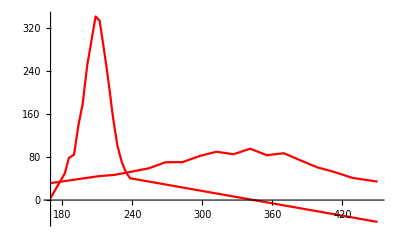

```mathematica
f=Sort[forward-Table[{0,MinimalBy[backward,Last][[1,2]]},{i,1,Length@forward}]];
b=Sort[backward-Table[{0,MinimalBy[backward,Last][[1,2]]},{i,1,Length@backward}]];
fp=Interpolation[forward,InterpolationOrder->1]
bp=Interpolation[backward,InterpolationOrder->1]
Plot[{fp[x],bp[x]},{x,170,450},PlotStyle->Red,PlotRange->Full]
```